ResourceFunction["MaTeXInstall"][]

```mathematica
<<MaTeX`
```

```mathematica
TempArray={0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105}
```

{0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105}

```mathematica
Tc=0.0867
```

0.0867

```mathematica
AvgCurvatureA ={0.086356,0.08637649,0.086721466,0.08724627,0.087914,0.08875,0.089779,0.090867,0.09194161,0.0928988,0.09375946,0.09449445,0.095199,0.0958655,0.0965585886,0.09731517,0.097048,0.09587,0.09465,0.0933848};
```

```mathematica
AvgCurvatureB={0.10278,0.10286,0.10292869,0.102899,0.10276046,0.10265122,0.10243219,0.1022195,0.10195380759,0.1016372,0.101263699,0.1008536,0.100364708,0.09978333,0.09910655,0.0981668,0.0970655,0.09588114,0.094656564,0.09338695};
```

```mathematica
AvgCurvatureC={0.10842671,0.1083257,0.1081403,0.107857,0.107484,0.106999,0.106431956,0.10575686,0.10500526878,0.104192186,0.103323224,0.10238584,0.1014168215379,0.10038726857,0.099319573,0.0982234688,0.0970662679,0.0958777,0.0946421829,0.093392159};
```

```mathematica
Dimensions[AvgCurvatureC]
```

{20}

```mathematica
betaArray = 1/TempArray;
```

```mathematica
curvxxGS=Table[1/AvgCurvatureA[[n]],{n,1,Dimensions[TempArray][[1]]}]
```

{11.58,11.5772,11.5312,11.4618,11.3748,11.2676,11.1385,11.0051,10.8765,10.7644,10.6656,10.5826,10.5043,10.4313,10.3564,10.2759,10.3042,10.4308,10.5652,10.7084}

```mathematica
curvxxES1=Table[1/AvgCurvatureB[[n]],{n,1,Dimensions[TempArray][[1]]}]
```

{9.72952,9.72195,9.71546,9.71827,9.73137,9.74173,9.76256,9.78287,9.80836,9.83892,9.87521,9.91536,9.96366,10.0217,10.0902,10.1867,10.3023,10.4296,10.5645,10.7081}

```mathematica
curvxxES2=Table[1/AvgCurvatureC[[n]],{n,1,Dimensions[TempArray][[1]]}]
```

{9.22282,9.23142,9.24725,9.27154,9.30371,9.34588,9.39567,9.45565,9.52333,9.59765,9.67837,9.76698,9.8603,9.96142,10.0685,10.1809,10.3022,10.43,10.5661,10.7075}

```mathematica
TBG=Tc*0.8
```

0.06936

```mathematica
w0=1;
```

```mathematica
wTBG=0.1;
```

```mathematica
scattRateArray = Table[w0+wTBG(Sqrt[Sqrt[1+(TempArray[[n]]/TBG)^4]]-1),{n,1,Dimensions[TempArray][[1]]}]
```

{1.00001,1.00005,1.00017,1.00042,1.00086,1.00158,1.00266,1.00416,1.00616,1.00869,1.01176,1.01536,1.01947,1.02404,1.02901,1.03432,1.03994,1.0458,1.05188,1.05813}

```mathematica
ρxx=curvxxGS*scattRateArray
```

{11.5801,11.5779,11.5332,11.4666,11.3846,11.2854,11.1681,11.0509,10.9435,10.8579,10.791,10.7452,10.7089,10.682,10.6568,10.6286,10.7157,10.9086,11.1133,11.3308}

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->30};
```

```mathematica
legend=SwatchLegend[{Blue,Green, Orange},{MaTeX["\\text{1 pocket}",Magnification->1.6],MaTeX["\\text{2 pocket}",Magnification->1.6],MaTeX["\\text{3 pocket}",Magnification->1.6]},LegendMarkers->Graphics[{EdgeForm[Black],Disk[]}],LegendMarkerSize->{16,16}];
```

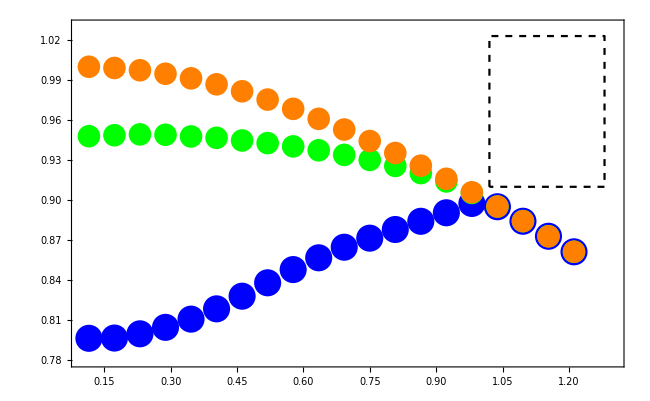

```mathematica
Legended[Show[ListPlot[Transpose@{TempArray/Tc,AvgCurvatureA/Max[AvgCurvatureC]},PlotStyle->{Blue,PointSize[0.03]},PlotRange->{{0.1,1.3},{0.78,1.03}}],ListPlot[Transpose@{TempArray/Tc,AvgCurvatureB/Max[AvgCurvatureC]},PlotStyle->{Green,PointSize[0.025]},BaseStyle->MaTeX],
ListPlot[Transpose@{TempArray/Tc,AvgCurvatureC/Max[AvgCurvatureC]},PlotStyle->{Orange,PointSize[0.025]},BaseStyle->MaTeX],
ListPlot[{{1.02,0.91},{1.02,1.023},{1.28,1.023},{1.28,0.91},{1.02,0.91}},Joined-> True,PlotStyle-> {Black,Dashed}],
Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2.7],MaTeX["C(T)",Magnification->2.7]},
BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,RotateLabel-> False,ImageSize->650],Placed[legend,Scaled[{0.88,0.75}]]]
```

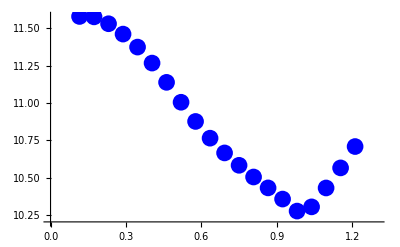

```mathematica
ListPlot[Transpose@{TempArray/Tc,curvxxGS},PlotStyle->{Blue,PointSize[0.03]},PlotRange->{{0,1.3},Automatic}]
```

```mathematica
displayLaTeX[string_]:=DisplayForm[ToBoxes@TraditionalForm@ToExpression[string,TeXForm,HoldForm]]
```

```mathematica
Min[ρxx]
```

10.6286

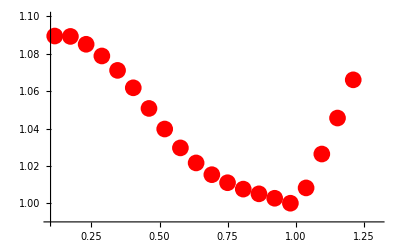

```mathematica
p1=ListPlot[Transpose@{TempArray/Tc,ρxx/Min[ρxx]},PlotStyle->{Red,PointSize[0.03]},PlotRange->{{0.1,1.3},{0.99,1.1}}]
```

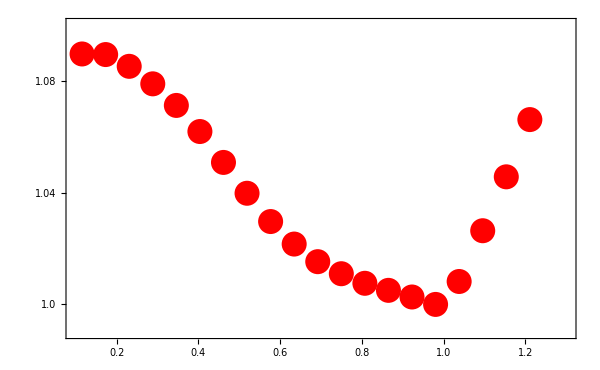

```mathematica
Show[p1,FrameTicks-> {{{{1.0,"1.0"},1.04,1.08},None},{Automatic,None}},Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->2.8],MaTeX["\\frac{\\rho_{xx}}{\\rho_\\text{min}}",Magnification->2.8]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600]
```